```mathematica
gray=RGBColor[0.7,0.7,0.7];
red=RGBColor[255/255,21/255,21/255];
SetDirectory[NotebookDirectory[]];
```

```mathematica
getTheoryData[pi_,pt_,pr_,pd_,n_]:=(
a=Import["FFM//output//diversity//diversity_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_.dat","Table"];
out={};
Do[
nnn=a[[i]][[-1]];
If[nnn<2&&i>61,Print["nnn error"<>ToString[i]]];
If[a[[i]][[2]]≠-1&&a[[i]][[1]]>61,AppendTo[out,{{a[[i]][[1]],a[[i]][[2*n]]},ErrorBar[a[[i]][[2*n + 1]]*√(nnn/(nnn-1))]}]],{i,1,1001}];
out
)
BP[n_]:=Max[n]/Total[n]
gini[x_]:=N[Sum[Sum[Abs[x[[i]]-x[[j]]],{j,1,Length[x]}],{i,1,Length[x]}]/(2*Length[x]*Sum[x[[j]],{j,1,Length[x]}])]
shannon[n_]:=(
Sh=0;
NN=Total[n];
Do[Sh-=n[[i]]/NN*Log[n[[i]]/NN],{i,1,Length[n]}];
N[Sh]
)
JE[n_]:=shannon[n]/Log[Length[n]]
TT[n_]:=Log[Length[n]]-shannon[n]
Sr[n_]:=(NN=Total[n];∑_(i=1)^Length[n] (n[[i]]/NN)^2)
H[n_]:=(nM=Mean[n];1/2*(∑_(i=1)^Length[n] Abs[n[[i]]-nM])/(∑_(i=1)^Length[n] n[[i]]))
```

## Fig A

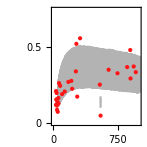

```mathematica
margins={0.9,0.5,1.2,0.4};
distance={0.6,0.6};
sizes={3*6/5,3*6/5};
fFigLegend[pi_,pt_,pr_,pd_]:=(
(*theory values*)
b=getTheoryData[pi,pt,pr,pd,8];

(*experimental values*)
fAll={};
f=BP;
Do[
c=Import["chambers/c"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,21}];
Do[
c=Import["chambers/s"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,11}];

(*add legends*)
xLegend=550;
yLegend1=0.14;
yLegend2=yLegend1-0.12*0.75;
yError=0.05*0.75;
AppendTo[b,{{xLegend,yLegend1},ErrorBar[yError]}];
AppendTo[fAll,{xLegend,yLegend2}];

(*plots*)
p1=ErrorListPlot[b,PlotRange->{{0,1000},{0,0.75}},PlotStyle->gray];
p2=ListPlot[fAll,PlotRange->{0,4},PlotStyle->{red,PointSize->Medium}];
p3=Show[{p1,p2},Frame->True,Axes->False];

p4=plot[
{p3(*fit[gam,pMax],*)},
xTicks->{0,250,500,750,1000},
yTicks->{0,0.25,0.5,0.75},
tickLength->0.12,
plotRange->{{0,1000},{0,0.75}},
plotDimensions->sizes,
plotMargins->margins,
plotLabels->{
Row[{Style["Cell number"]}],
Row[{Style["Largest cluster fractional size"]}]},
labelsDistance->{0.5,0.85},
plotTitle->True,
titleText->Row[{Style[""]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)
figA=fFigLegend["0.0001",0.7,"0.158114",0.026];
t1=Style["Theory",FontSize->6,FontFamily->"Helvetica",gray];
t2=Style["Experiment",FontSize->6,FontFamily->"Helvetica",red];
ddx=0.2;
FigA=figure[6,5,
elements->{figA,t1,t2},
elementCoordinates->{
{0,0},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(0.75-yLegend1)/0.75*3*6/5},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(0.75-yLegend2)/0.75*3*6/5}
},
yCenteredElements->{2,3}]
```

## Fig B-G

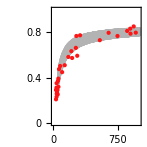

```mathematica
margins={0.9,0.5,1.2,0.4};
distance={0.6,0.6};
sizes={3*6/5,3*6/5};
fFig[pi_,pt_,pr_,pd_,f_,n_,yLabel_,yLabelDistance_,yRange_,yTicksList_]:=(
(*theory values*)
b=getTheoryData[pi,pt,pr,pd,n];

(*experimental values*)
fAll={};
Do[
c=Import["chambers/c"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,21}];
Do[
c=Import["chambers/s"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,11}];

(*plots*)
p1=ErrorListPlot[b,PlotRange->{{0,1000},yRange},PlotStyle->gray];
p2=ListPlot[fAll,PlotRange->{{0,1000},yRange},PlotStyle->{red,PointSize->Medium}];
p3=Show[{p1,p2},Frame->True,Axes->False];

p4=plot[
{p3(*fit[gam,pMax],*)},
xTicks->{0,250,500,750,1000},
yTicks->yTicksList,
tickLength->0.12,
plotRange->{{0,1000},yRange},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{0.9,0.5,1.2,0.4},
plotLabels->{
Row[{Style["Cell number"]}],
yLabel},
labelsDistance->{0.5,yLabelDistance},
plotTitle->True,
titleText->Row[{Style[""]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)

FigB=fFig["0.0001",0.7,"0.158114",0.026,
gini,
1,
Row[{
Style["Gini coefficient "],Style["G",Italic]
}],
0.75,
{0,1},
{0,0.2,0.4,0.6,0.8,1}
]
```

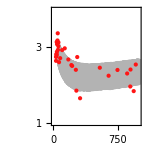

```mathematica
FigC=fFig["0.0001",0.7,"0.158114",0.026,
shannon,
2,
Row[{
Style["Shannon index "],Style["Sh",Italic]
}],
0.55,
{1,4},
{1,2,3,4}
]
```

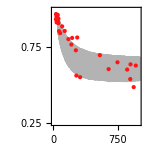

```mathematica
FigD=fFig["0.0001",0.7,"0.158114",0.026,
JE,
4,
Row[{
Style["Evenness "],Subscript[Style["J",Italic],Style["E",FontSize->5]]
}],
0.85,
{0.25,1},
{0.25,0.5,0.75,1}
]
```

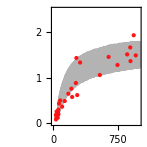

```mathematica
FigE=fFig["0.0001",0.7,"0.158114",0.026,
TT,
5,
Row[{
Style["Theil index "],Style["T",Italic]
}],
0.75,
{0,2.5},
{0,0.5,1,1.5,2,2.5}
]
```

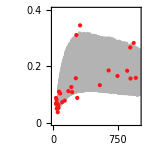

```mathematica
FigF=fFig["0.0001",0.7,"0.158114",0.026,
Sr,
6,
Row[{
Style["Simpson's index "],Subscript[Style["S",Italic],Style["r",FontSize->5]]
}],
0.75,
{0,0.4},
{0,0.2,0.4}
]
```

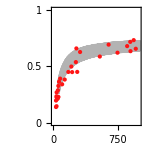

```mathematica
FigG=fFig["0.0001",0.7,"0.158114",0.026,
H,
9,
Row[{
Style["Hoover index "],Style["H",Italic]
}],
0.85,
{0,1},
{0,0.25,0.5,0.75,1}
]
```

## Figure

```mathematica
fLegend=6;
t1=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["i",FontFamily->"Arial",FontSize->4]],Style[StringJoin[" = 0.0001"],FontFamily->"Arial",FontSize->fLegend]}];
t2=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["t",FontFamily->"Arial",FontSize->4]],Style[StringJoin[" = 0.7"],FontFamily->"Arial",FontSize->fLegend]}];
t3=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["r",FontFamily->"Arial",FontSize->4]],Style[" = 0.1581",FontFamily->"Arial",FontSize->fLegend]}];
t4=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["c",FontFamily->"Arial",FontSize->4]],Style[StringJoin[" = 0.026"],FontFamily->"Arial",FontSize->fLegend]}];
center={0.1,0};
dxx={0,-0.29};
l1a=figure[
1.8,
1.4,
elements->{t1,t2,t3,t4},
elementCoordinates->{center,center+1*dxx,center+2*dxx,center+3*dxx}]
```

-Graphics-

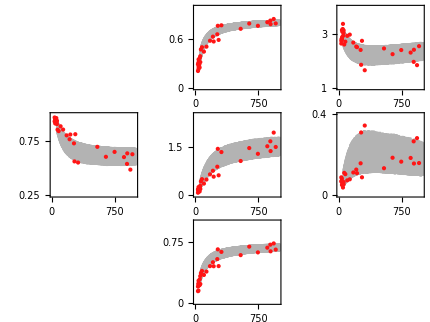

```mathematica
x0=0;
y0=0;
dx=5;
dy=-4.7;
dy0=-0.1;
dxLet=0.;
dx0=-0.1;
FigED4=figure[
15.2,
9.5*3/2,
elements->{
FigA,FigB,FigC,FigD,FigE,FigF,FigG,l1a},
elementCoordinates->{
{0*dx+dx0,0*dy-dy0},{1*dx+dx0,0*dy-dy0},{2*dx+dx0,0*dy-dy0},
{0*dx+dx0,1*dy-dy0},{1*dx+dx0,1*dy-dy0},{2*dx+dx0,1*dy-dy0},
{1*dx+dx0,2*dy-dy0},
{0*dx+dx0,0*dy-dy0}+{3.45,-0.5499999999999998}+{0,0.4-0.3}},
letters->{
Style["a",FontFamily->"Helvetica",FontSize->8,Bold],
Style["b",FontFamily->"Helvetica",FontSize->8,Bold],
Style["c",FontFamily->"Helvetica",FontSize->8,Bold],
Style["d",FontFamily->"Helvetica",FontSize->8,Bold],
Style["e",FontFamily->"Helvetica",FontSize->8,Bold],
Style["f",FontFamily->"Helvetica",FontSize->8,Bold],
Style["g",FontFamily->"Helvetica",FontSize->8,Bold]
},
letterCoordinates->{{0*dx+dxLet,0*dy},{1*dx+dxLet,0*dy},{2*dx+dxLet,0*dy},{0*dx+dxLet,1*dy},{1*dx+dxLet,1*dy},{2*dx+dxLet,1*dy},{1*dx+dxLet,2*dy}},
(*letters->{"A","B","C","D","E","F","G","H"}(*list of letters for the figure elements, as strings, e.g. {"a)","b)","c)"}, or {"A","B"}*),
letterCoordinates->{{0*dx,0*dy},{1*dx,0*dy},{2*dx,0*dy},{0*dx,1*dy},{1*dx,1*dy},{2*dx,1*dy},{0.5*dx,2*dy},{1.5*dx,2*dy}}(**),*)
centeredElements->{}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figs//SYS_ED_Fig2.pdf",FigED4]
```

figs//SYS_ED_Fig2.pdf